```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_Tiingo/";*)
```

```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BTCUSD_BTCUSD_25SEP20/";
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

-Graphics-

```mathematica
F2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[FNIG[x-z,α,β,μ1,δ1] FNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

Make density out of cdf

-Graphics-

```mathematica
f2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[fNIG[x-z,α,β,μ1,δ1] fNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

```mathematica
Timing[F2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{7.12192,0.547637}

```mathematica
Timing[f2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{0.016338,0.3921}

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},n=Length[s];If[Length[x]==0,N[Length[Select[s,#1≤x&]]/(n+1)],Table[N[Length[Select[s,#1≤x⟦k⟧&]]/(n+1)],{k,1,Length[x]}]]]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

```mathematica
data[[1;;10]]
```

( | datetime | spot | futures | rs | rf
0 | 2020-06-17 01:00:00 | 9479.56 | 9568.25 | -0.00502031 | -0.00484805
1 | 2020-06-17 02:00:00 | 9455.49 | 9542.25 | -0.00254238 | -0.00272102
2 | 2020-06-17 03:00:00 | 9439.89 | 9530.25 | -0.0016512 | -0.00125836
3 | 2020-06-17 04:00:00 | 9453.3 | 9549.5 | 0.00141956 | 0.00201785
4 | 2020-06-17 05:00:00 | 9459.25 | 9550.5 | 0.000629212 | 0.000104712
5 | 2020-06-17 06:00:00 | 9439.4 | 9523.75 | -0.00210068 | -0.00280483
6 | 2020-06-17 07:00:00 | 9472.49 | 9572.75 | 0.00349939 | 0.00513184
7 | 2020-06-17 08:00:00 | 9506.24 | 9613.5 | 0.00355662 | 0.00424784
8 | 2020-06-17 09:00:00 | 9490.43 | 9588.25 | -0.0016645 | -0.00262997)

```mathematica
data[[1,5]]
```

rs

```mathematica
data[[1,6]]
```

rf

```mathematica
tmp=Import[NotebookDirectory[] <> "data_btc_hourly/" <> ToString[kk] <> "_parameters.csv"]
```

(2020-06-17-01-00-00
0.918711
0.0675779
0.83696)

```mathematica
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
```

```mathematica
u=hatF[data[[2;;,5]]];
v=hatF[data[[2;;,6]]];
```

Attempt to determine LL from simulated data turns out to be very noisy

```mathematica
tmp=Import[NotebookDirectory[] <> "data_btc_hourly/" <> ToString[kk] <> "_simulation.csv"];
```

```mathematica
tmp[[1;;10]]
```

(0.0711586 | 0.0251395
0.0154797 | 0.0150197
0.433331 | 0.402732
0.49447 | 0.422992
0.897262 | 0.891002
0.909222 | 0.951261
0.97502 | 0.966461
0.571429 | 0.472971
0.709546 | 0.749845
0.98706 | 0.98916)

```mathematica
Dimensions[tmp]
```

{50000,2}

```mathematica
uv=tmp;
skd=SmoothKernelDistribution[uv];
```

-Graphics-

copula density

```mathematica
c2NIG[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ]:=Module[{x,y},
x=NIGInv[u,α,β];
y=NIGInv[v,α,β];
f2NIG[x,y,α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ] / (NIGPDF[x,α,β] NIGPDF[y,α,β])
]
```

```mathematica
Timing[c2NIG[0.5,0.1,5,0,0.2]]
```

{0.510025,0.998887}

-Graphics-

-Graphics-

```mathematica
c2NIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{13.7846,8.21304,3.50562,3.31774,2.48741}

```mathematica
PDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{5.3424,4.56473,3.30099,3.42435,2.63553}

```mathematica
CNIG[u_,v_,α_,β_,δ_]:=F2NIG[NIGInv[u,α,β],NIGInv[v,α,β],α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ]
```

```mathematica
CNIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{0.0406065,0.139059,0.240148,0.705553,0.509356}

```mathematica
CDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{0.0293662,0.12861,0.234006,0.699649,0.505086}

```mathematica
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)]
```

325.368

```mathematica
%/Length[data]
```

0.965484

```mathematica
Timing[Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)]]
```

{17.4347,401.509}

```mathematica
%/Length[data]
```

{0.051735,1.19142}

```mathematica
tLL={};
mLL={};
For[kk=0, kk<=185, kk++,
Print[kk];
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,5]]];
v=hatF[data[[2;;,6]]];
tmp=Import[NotebookDirectory[] <> "data_btc_hourly/" <> ToString[kk] <> "_parameters.csv"];
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
ll=Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLL, ll];
AppendTo[mLL,mll];
]
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {5.02409}. NIntegrate obtained 0.00615512 and 3.59895×10^-8 for the integral and error estimates.

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {4.44727}. NIntegrate obtained 0.00666357 and 1.96944×10^-8 for the integral and error estimates.

47

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {5.09582}. NIntegrate obtained 0.00517615 and 1.15107×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

48

49

50

51

52

53

54

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

55

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

```mathematica
(*tLLnew={};
mLLnew={};
For[kk=0, kk<=111, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
uv=Import[NotebookDirectory[] <> "data_xrp/" <> ToString[kk] <> "_simulation.csv"];
skd=SmoothKernelDistribution[uv];
ll=
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLnew, ll];
AppendTo[mLLnew,mll];
]*)
```

```mathematica
tLL
```

{401.509,398.879,397.883,399.664,394.517,390.116,386.287,381.61,378.688,380.486,384.334,376.04,378.571,382.956,382.408,377.048,374.659,369.109,369.416,365.126,372.927,372.383,373.725,381.223,375.959,377.73,367.833,370.322,365.292,360.752,357.671,354.604,353.379,362.049,359.172,358.903,355.357,354.408,351.95,351.321,350.364,352.406,351.365,352.617,357.089,355.893,338.537,352.957,353.725,356.579,354.58,355.488,348.754,326.823,295.1,289.994,288.646,320.977,332.352,333.787,326.009,303.462,306.513,309.103,306.814,303.135,326.516,330.619,328.526,331.736,338.781,335.615,327.932,343.893,346.079,341.497,330.711,335.719,311.004,336.548,333.089,334.485,329.617,333.695,327.982,318.761,334.571,326.513,303.879,306.421,332.538,334.642,338.559,340.365,303.1,323.236,299.722,297.474,297.745,297.969,314.471,337.258,308.035,309.392,284.063,308.643,310.367,334.553,332.96,331.05,332.665,336.056,341.279,341.239,344.796,346.262,336.87,336.341,313.52,324.466,339.159,336.015,344.215,324.583,336.817,334.434,343.252,350.206,349.087,347.848,336.147,332.274,316.024,316.601,313.379,313.606,320.642,306.013,304.016,306.76,328.383,332.606,331.792,324.604,308.051,328.381,325.601,312.054,307.666,297.238,305.796,283.649,306.327,344.97,357.749,368.004,362.951,367.622,356.336,361.883,360.646,367.111,378.098,371.929,368.941,339.593,365.369,365.581,376.745,370.436,389.98,384.508,368.392,390.399,340.172,351.803,391.149,393.127,398.002,402.934,414.29,400.605,404.525,407.271,410.621,416.124}

```mathematica
mLL
```

{1.19142,1.18362,1.18066,1.18595,1.17067,1.15762,1.14625,1.13237,1.1237,1.12904,1.14046,1.11584,1.12336,1.13637,1.13474,1.11884,1.11175,1.09528,1.09619,1.08346,1.10661,1.10499,1.10897,1.13122,1.11561,1.12086,1.09149,1.09888,1.08395,1.07048,1.06134,1.05224,1.0486,1.07433,1.06579,1.06499,1.05447,1.05166,1.04436,1.0425,1.03965,1.04571,1.04263,1.04634,1.05961,1.05606,1.00456,1.04735,1.04963,1.0581,1.05217,1.05486,1.03488,0.969801,0.875668,0.860516,0.856518,0.952454,0.986209,0.990465,0.967386,0.900481,0.909534,0.917219,0.910429,0.899511,0.96889,0.981066,0.974854,0.984381,1.00528,0.995889,0.973093,1.02045,1.02694,1.01335,0.981337,0.996199,0.922859,0.998659,0.988394,0.992537,0.978093,0.990193,0.973239,0.94588,0.992792,0.968882,0.901717,0.909261,0.986761,0.993004,1.00463,1.00999,0.899406,0.959158,0.889383,0.882713,0.883517,0.884182,0.933149,1.00076,0.914051,0.918078,0.842916,0.915854,0.920971,0.992738,0.988011,0.982343,0.987138,0.9972,1.0127,1.01258,1.02313,1.02748,0.999613,0.998044,0.930325,0.962808,1.00641,0.997079,1.02141,0.963153,0.999456,0.992386,1.01855,1.03919,1.03587,1.03219,0.99747,0.985977,0.937757,0.939469,0.929907,0.930581,0.95146,0.90805,0.902124,0.910268,0.974431,0.986962,0.984546,0.963217,0.914099,0.974426,0.966174,0.925977,0.912956,0.882013,0.907407,0.841687,0.908981,1.02365,1.06157,1.092,1.07701,1.09087,1.05738,1.07384,1.07016,1.08935,1.12195,1.10365,1.09478,1.00769,1.08418,1.08481,1.11794,1.09922,1.15721,1.14097,1.09315,1.15845,1.00941,1.04393,1.16068,1.16655,1.18101,1.19565,1.22935,1.18874,1.20037,1.20852,1.21846,1.23479}

```mathematica
Export[NotebookDirectory[] <> "data_btcLL_hourly_NIG_btc.csv", Prepend[{Range[0,185],tLL, mLL}ᵀ, {"", "LL", "mean LL"}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/data_btcLL_hourly_NIG_btc.csv

```mathematica
(*Export[NotebookDirectory[] <> "data_xrp/LL_NIG_new.csv", Prepend[{Range[0,87],tLLnew, mLLnew}ᵀ, {"", "LL", "mean LL"}]]*)
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/data/LL_NIG_new.csv

Gaussian copula

```mathematica
LLg[x_]:=Log[PDF[BinormalDistribution[{0,0}, {1,1}, ρ], x]]-Total[Log[PDF[NormalDistribution[],#]&/@x]]
```

```mathematica
ρ=0.9907220113152815;
ρ=0.9891018086831789;
```

```mathematica
tLLg={};
mLLg={};
For[kk=1, kk<=1, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLg[{InverseCDF[NormalDistribution[],#[[1]]],InverseCDF[NormalDistribution[],#[[2]]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLg, ll];
AppendTo[mLLg,mll];
]
```

```mathematica
tLLg
```

{365.689}

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Z=RandomVariate[NormalDistribution[],{100000,2}];
```

```mathematica
X=Z[[;;,1]];
Y=ρ Z[[;;,1]] + Sqrt[1-ρ^2] Z[[;;,2]];
```

```mathematica
U=hatF[X];
V=hatF[Y];
```

```mathematica
skd=SmoothKernelDistribution[{U,V}ᵀ];
ll=
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)];
```

```mathematica
ll
```

382.909

Clayton copula

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

```mathematica
LLc[u_]:=Log[PDF[𝒟, u]]-Total[Log[#&/@u]]
```

```mathematica
c=40;
```

```mathematica
tLLc={};
mLLc={};
For[kk=18, kk<=18, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLc[{#[[1]],#[[2]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLc, ll];
AppendTo[mLLc,mll];
]
```

```mathematica
tLLc
```

{548.926}

```mathematica
mLLc
```

{1.82367}

```mathematica
Quantile[𝒟, {0.5, 0.5}]
```

Quantile[CopulaDistribution[{Clayton,1/40},{UniformDistribution[{0,1}],UniformDistribution[{0,1}]}],{0.5,0.5}]

-Graphics-

```mathematica
ClaytonCDF[u_,v_]:=(u^-c+v^-c-1)^(-1/c)
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

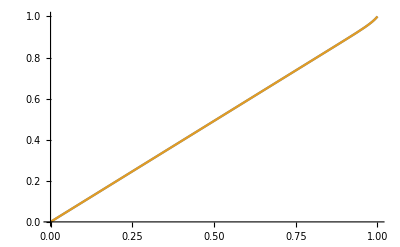

```mathematica
Plot[{CDF[𝒟, {u,u}],ClaytonCDF[u,u]}, {u,0,1}]
```

```mathematica
Simplify[ClaytonCDF[q,q]/q]
```

1/((2/q^40-1)^(1/40) q)

```mathematica
Simplify[CDF[𝒟,{q,q}]/q, Assumptions->0<q<1]
```

1/((2-q^40)^(1/40))

```mathematica
QD[q_?NumericQ]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
QD2[q_?NumericQ]:=
If[0<q≤0.5, ClaytonCDF[q,q]/q,(1-2q+ ClaytonCDF[q,q])/(1-q)]
```

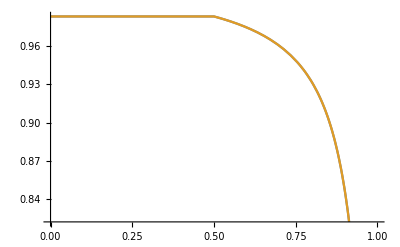

```mathematica
Plot[{QD[q],QD2[q]}, {q,0,1}]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
kk=18;
```

```mathematica
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
```

```mathematica
Clear[c, QD,𝒟]
```

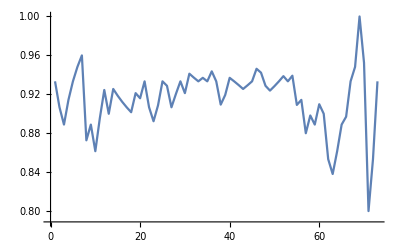

```mathematica
ListPlot[Table[QDemp[q, u, v], {q,0.05,0.95, 0.0125}],Joined->True]
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
QD[q_]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
target=Table[QDemp[q, u, v], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[target, KendallTau[u,v]];
target
```

{0.933333,0.933333,1.,0.933333,0.884563}

```mathematica
f= Table[QD[q], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[f, c/(c+2)]; (* Kendall's tau *)
Sqrt[Total[(target-f)^2]]
```

√((0.933333-20. (2 0.05^-c-1)^(-1/c))^2+(0.933333-10. (2 0.1^-c-1)^(-1/c))^2+(1.-10. ((2 0.9^-c-1)^(-1/c)-0.8))^2+(0.933333-20. ((2 0.95^-c-1)^(-1/c)-0.9))^2+(0.884563-c/(c+2))^2)

```mathematica
NMinimize[{Sqrt[Total[(target-f)^2]], c>0}, c]
```

{0.141561,{c→181.081}}

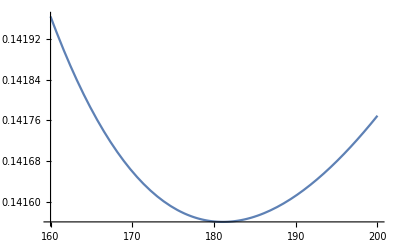

```mathematica
Plot[Sqrt[Total[(target-f)^2]], {c,160,200}]
```